```mathematica
Clear["Global`*"]

(* Fitting a GARCH Process to Financial Time Series Data *)
(* e.g. CCJ: Cameco Corporation *)

ccj=TimeSeries[FinancialData["NYSE:CCJ","Return",{{2000,1,1},{2016,1,1}}],TemporalRegularity->True]
```

TimeSeries[…]

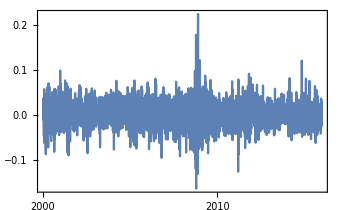

```mathematica
DateListPlot[ccj,PlotRange->All]
```

```mathematica
model=TimeSeriesModelFit[ccj,"GARCH"]
```

TimeSeriesModel[…]

```mathematica
eproc=model["BestFit"]
```

GARCHProcess[0.0000100931,{0.0692851},{0.915936}]

```mathematica
quan=Quantile[NormalDistribution[0,1],0.95]
```

1.64485

```mathematica
VaR=MovingMap[Sqrt[(Mean[#^2]-(Mean[#])^2)]*quan &,ccj,10]
```

TimeSeries[…]

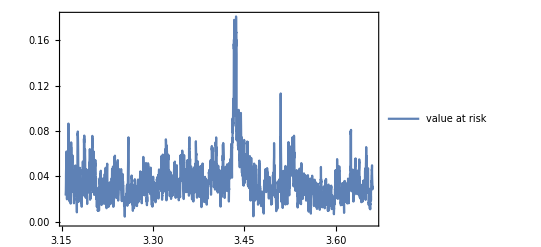

```mathematica
DateListPlot[VaR,PlotRange->All,PlotLegends->{"value at risk"}]
```